Tapp 1.84: With a computer algebra system, implement the construction in the proof of Theorem 1.65 to graph a plane curve whose signed curvature function is:

(1) κ(t) = -t

integrating κ give -(1.5)t^2

```mathematica
θ[t_]:= -0.5*t^2
vx[t_]:= Cos[θ[t]]
vy[t_]:= Sin[θ[t]]

x[t_]:=NIntegrate[vx[s],{s, 0, t}]
y[t_] := NIntegrate[vy[s], {s, 0, t}]
```

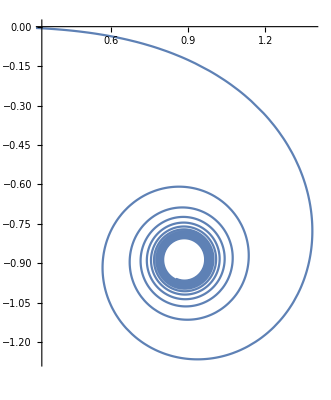

```mathematica
ParametricPlot[{NIntegrate[vx[s],{s, 0, t}], NIntegrate[vy[s], {s, 0, t}]}, {t, 0, 4π}]
```

(2) κ(t) = -2 t^2

Integrating κ gives -(2/3)t^3

```mathematica
ClearAll[θ, vx, vy, x, y]
```

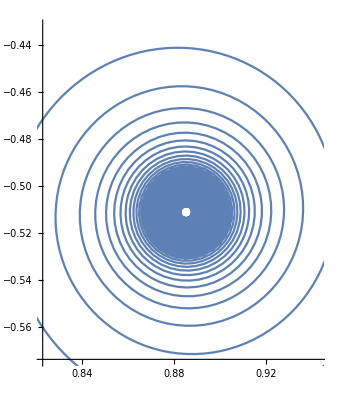

```mathematica
θ[t_]:= (-2/3)*t^3
vx[t_]:= Cos[θ[t]]
vy[t_]:=Sin[θ[t]]
ParametricPlot[{NIntegrate[vx[s],{s, 0, t}], NIntegrate[vy[s], {s, 0, t}]}, {t, 0, 4π}]
```

(3) κ(t) = c*sin(t) for several choices of c>0 and find a value of c for which the curve appears periodic

Integrating csin(t) gives -ccos(t)

π

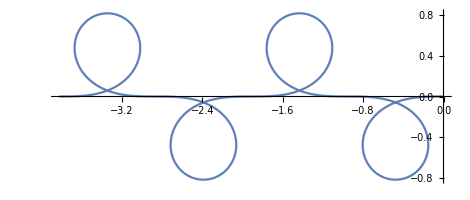

```mathematica
ClearAll[θ, vx, vy, x, y]
c = π
θ[t_]:= -c*Cos[t]
vx[t_]:= Cos[θ[t]]
vy[t_]:= Sin[θ[t]]
ParametricPlot[{NIntegrate[vx[s],{s, 0, t}], NIntegrate[vy[s], {s, 0, t}]}, {t, 0, 4π}]
```

5

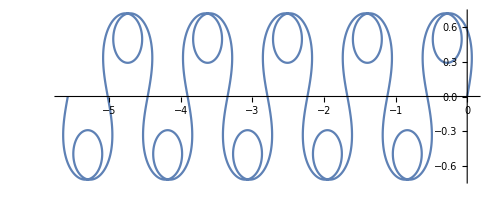

```mathematica
ClearAll[θ, vx, vy, x, y]
c = 5
θ[t_]:= -c*Cos[t]
vx[t_]:= Cos[θ[t]]
vy[t_]:= Sin[θ[t]]
ParametricPlot[{NIntegrate[vx[s],{s, 0, t}], NIntegrate[vy[s], {s, 0, t}]}, {t, 0, 10π}]
```

10 π

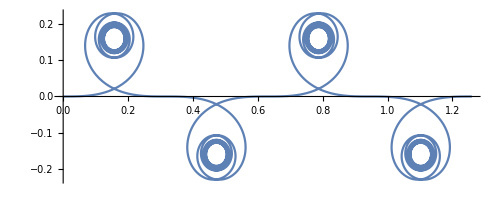

```mathematica
ClearAll[θ, vx, vy, x, y]
c = 10*π
θ[t_]:= -c*Cos[t]
vx[t_]:= Cos[θ[t]]
vy[t_]:= Sin[θ[t]]
ParametricPlot[{NIntegrate[vx[s],{s, 0, t}], NIntegrate[vy[s], {s, 0, t}]}, {t, 0, 4π}]
```

I’m not sure what is meant by a periodic curve. Each of these looks periodic (in the sense that it repeats in space) despite being different values and vastly different shapes. None of these curves appear closed.

(4) κ(t) = t * sin(t)

```mathematica
Integrating tsin(t) gives sin(t)+tcos(t)
```

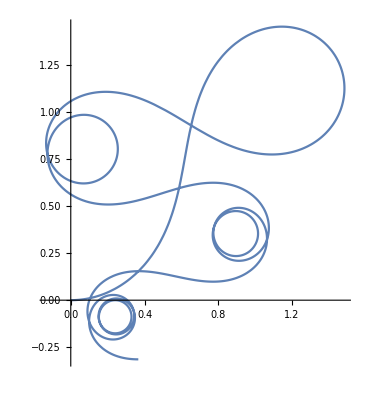

```mathematica
ClearAll[θ, vx, vy, x, y]
θ[t_]:= Sin[t] + t*Cos[t]
vx[t_]:= Cos[θ[t]]
vy[t_]:= Sin[θ[t]]
ParametricPlot[{NIntegrate[vx[s],{s, 0, t}], NIntegrate[vy[s], {s, 0, t}]}, {t, 0, 4π}]
```

(5) κ(t) = e^t

integrating e^t gives e^t

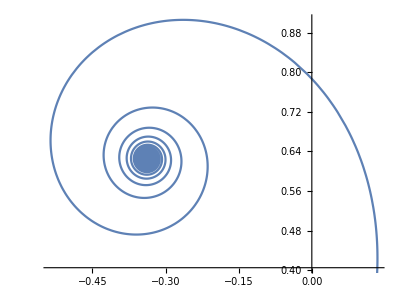

```mathematica
ClearAll[θ, vx, vy, x, y]
θ[t_]:=Exp[t]
vx[t_]:= Cos[θ[t]]
vy[t_]:= Sin[θ[t]]
ParametricPlot[{NIntegrate[vx[s],{s, 0, t}], NIntegrate[vy[s], {s, 0, t}]}, {t, 0, 2π}]
```